# Calcolo della risposta al gradino per un sistema LTI-TC (caso poli complessi e coniugati)

Fdt del sistema

```mathematica
G[s_]:=(s-1)/(s^3+8 s^2+25 s+26)
```

Poli del sistema (ci danno una informazione in merito ai modi naturali “visibili” lato uscita)

```mathematica
Solve[Denominator[G[s]]==0,s]
```

{{s→-3-2 ⅈ},{s→-3+2 ⅈ},{s→-2}}

Calcolo la risposta forzata in s al gradino unitario

```mathematica
Subscript[Y, f][s_]:=G[s](1/s)
```

```mathematica
Subscript[Y, f][s]
```

(-1+s)/(s (26+25 s+8 s^2+s^3))

```mathematica
Apart[Subscript[Y, f][s]]
```

-1/(26 s)+3/(10 (2+s))+(-63-17 s)/(65 (13+6 s+s^2))

Scrivo in maniera “verbosa” la Yf[s] mettendo in evidenza i quattro fratti semplici

```mathematica
Subscript[C, 1](1/s)+Subscript[C, 2](1/(s+2))+Subscript[C, 3](1/(s+3-2ⅈ))+Subscript[C, 4](1/(s+3+2ⅈ))
```

C_1/s+C_2/(2+s)+C_3/((3-2 ⅈ)+s)+C_4/((3+2 ⅈ)+s)

Formula di Heaviside semplificata per il calcolo dei coefficienti Ci

```mathematica
Subscript[C, 1]=lim_(s->0) s Subscript[Y, f][s]
```

-1/26

```mathematica
Subscript[C, 2]=lim_(s->-2) (s+2) Subscript[Y, f][s]
```

3/10

```mathematica
Subscript[C, 3]=lim_(s->-3+2ⅈ) (s+3-2ⅈ) Subscript[Y, f][s]
```

-17/130+(3 ⅈ)/65

```mathematica
Subscript[C, 4]=Conjugate[Subscript[C, 3]]
```

-17/130-(3 ⅈ)/65

```mathematica
Subscript[C, 1](1/s)+Subscript[C, 2](1/(s+2))+Subscript[C, 3](1/(s+3-2ⅈ))+Subscript[C, 4](1/(s+3+2ⅈ))
```

-1/(26 s)+3/(10 (2+s))-(17/130-(3 ⅈ)/65)/((3-2 ⅈ)+s)-(17/130+(3 ⅈ)/65)/((3+2 ⅈ)+s)

```mathematica
F[Z_,γ_,t_]:=ComplexExpand[Re[Z Exp[I γ t]]]
```

```mathematica
Subscript[y, f][t_]:=Subscript[C, 1] UnitStep[t]+Subscript[C, 2] Exp[-2 t]UnitStep[t]+2 Exp[-3t]F[Subscript[C, 3],2,t]UnitStep[t]
```

```mathematica
Subscript[y, f][t]
```

-UnitStep[t]/26+3/10 ⅇ^(-2 t) UnitStep[t]+2 ⅇ^(-3 t) (-17/130 Cos[2 t]-3/65 Sin[2 t]) UnitStep[t]

```mathematica
Simplify[ComplexExpand[InverseLaplaceTransform[Subscript[Y, f][s],s,t]]]
```

-1/130 ⅇ^(-3 t) (-39 ⅇ^t+5 ⅇ^(3 t)+34 Cos[2 t]+12 Sin[2 t])

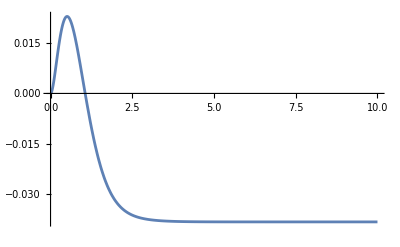

```mathematica
Plot[Subscript[y, f][t],{t,0,10},PlotRange->All]
```